# A Socio-Economic Analysis of FRC Team Performance

## Jacob Lessing

```mathematica
champd=Import["https://frc-events.firstinspires.org/2018/CMPMI","Data"];
 (champd=Interpreter["Integer"]@champd[[2,2,2]][[All,1]])//Short;
```

```mathematica
champh=Import["https://frc-events.firstinspires.org/2018/CMPTX","Data"];
 (champh=Interpreter["Integer"]@champh[[2,2,2]][[All,1]])//Short;
```

```mathematica
(champteams=Union[champd,champh]) //Short
```

{16,20,25,27,33,45,51,56,58,59,67,«788»,7225,7226,7250,7277,7287,7293,7301,7303,7312,7327,7329}

```mathematica
data=Flatten[Import["teamnumberaddressisolateddata.xlsx","Data"],1]//Rest;
```

```mathematica
teamnumberlist=Interpreter["Integer"]@data[[All,1]];
```

```mathematica
assoc=Association[Table[Rule[data[[n]][[1]],data[[n]][[2]]],{n,1,Length@data}]];
```

```mathematica
(assoc=(StringCases[#,DigitCharacter..]&)/@assoc)//Short
```

<|1.→{48340},4.→{91406},8.→{94301},«3782»,2.02001×10^8→{48033},2.02001×10^8→{76133}|>

```mathematica
assoc=Map[Interpreter["Integer"],assoc];
```

```mathematica
assoc=KeyMap[Interpreter["Integer"],assoc]
```

<|1→{48340},4→{91406},8→{94301},11→{7836},16→{72653},20→{12065},21→{32796},23→{2360},25→{8902},27→{48346},28→{11963},31→{74037},3763,202000549→{49620},202000557→{3561},202000564→{39120},202000575→{49070},202000576→{93648},202000579→{90031},202000583→{90001},202000590→{96817},202000607→{75074},202000618→{85139},202000631→{48033},202000633→{76133}|>
 |  |  |  |

```mathematica
teamnumbertozipassoc=assoc;
```

```mathematica
data2=Flatten[Import["zipincomeisolateddata.xlsx","Data"],1]//Rest//Interpreter["Integer"];
```

```mathematica
assoc2=Association[Table[Rule[data2[[n]][[1]],data2[[n]][[2]]],{n,1,Length@data2}]];
```

```mathematica
ziptoincomeassoc=assoc2
```

<|601→11757,602→16190,603→16645,606→13387,610→18741,612→17744,616→14918,617→17157,622→16727,623→16401,624→16832,627→17579,631→9632,637→15736,638→14448,641→16292,30908,99832→67917,99833→63490,99835→70765,99836→66875,99840→70673,99841→59688,99901→67321,99918→63125,99919→50956,99921→58047,99922→31250,99925→48646,99926→57969,99927→17981,99929→55742|>
 |  |  |  |

```mathematica
full=Table[Association[
"team"->teamnumberlist[[n]],
"zip"->teamnumbertozipassoc[teamnumberlist[[n]]][[1]],
"income"->ziptoincomeassoc[teamnumbertozipassoc[teamnumberlist[[n]]][[1]]],
"qualified"->If[MemberQ[champteams,teamnumberlist[[n]]],"Y","N"]],{n,1,Length@teamnumberlist,1}]
dataset=full//Dataset
```

{<|team→1,zip→48340,income→33292,qualified→N|>,<|team→4,zip→91406,income→51564,qualified→N|>,<|team→8,zip→94301,income→146488,qualified→N|>,3782,<|team→202000631,zip→48033,income→47326,qualified→N|>,<|team→202000633,zip→76133,income→52583,qualified→N|>}
 |  |  |  |

Dataset[<>]

```mathematica
{16,20,25,27,33,45,51,56,58,59,67,70,71,74,78,85,«778»,7173,7179,7190,7193,7198,7225,7226,7250,7277,7287,7293,7301,7303,7312,7327,7329}
```

```mathematica
dataset[Select[#income>150000&],"team"]//Length
```

57

```mathematica
dataset[#zip&]
```

Failure[…]

```mathematica
(dataset[Select[#team<=4950&],"income"]//Length) / (dataset[Select[#team>4950&],"income"]//Length )
```

1893/1894

```mathematica
labels={{Style["# of teams from a zipcode with that income",Bold],""},{Style["median household income of team's home zipcode ($)",Bold],Style["Seniority Analysis of Team Income",{Bold,Large}] ""}};
```

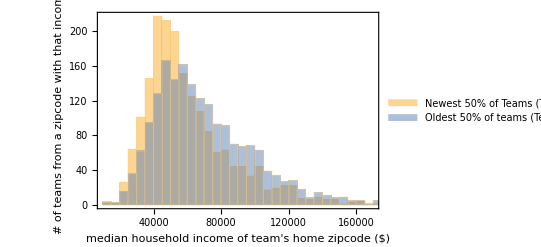

```mathematica
Histogram[{(dataset[Select[#team>4950&],"income"]//Normal),(dataset[Select[#team<=4950&],"income"]//Normal)},Frame->True,FrameLabel->labels,LabelStyle->"Subsection", ChartLegends->{"Newest 50% of Teams\n(Team # > 4950, n = 1894)","Oldest 50% of teams\n(Team # <= 4950, n = 1893)"}]
```

{{0,17.},{20000,13.},{40000,13.},{60000,20.},{80000,24.},{100000,25.},{120000,30.},{140000,24.},{160000,26.},{180000,38.},{200000,0}}

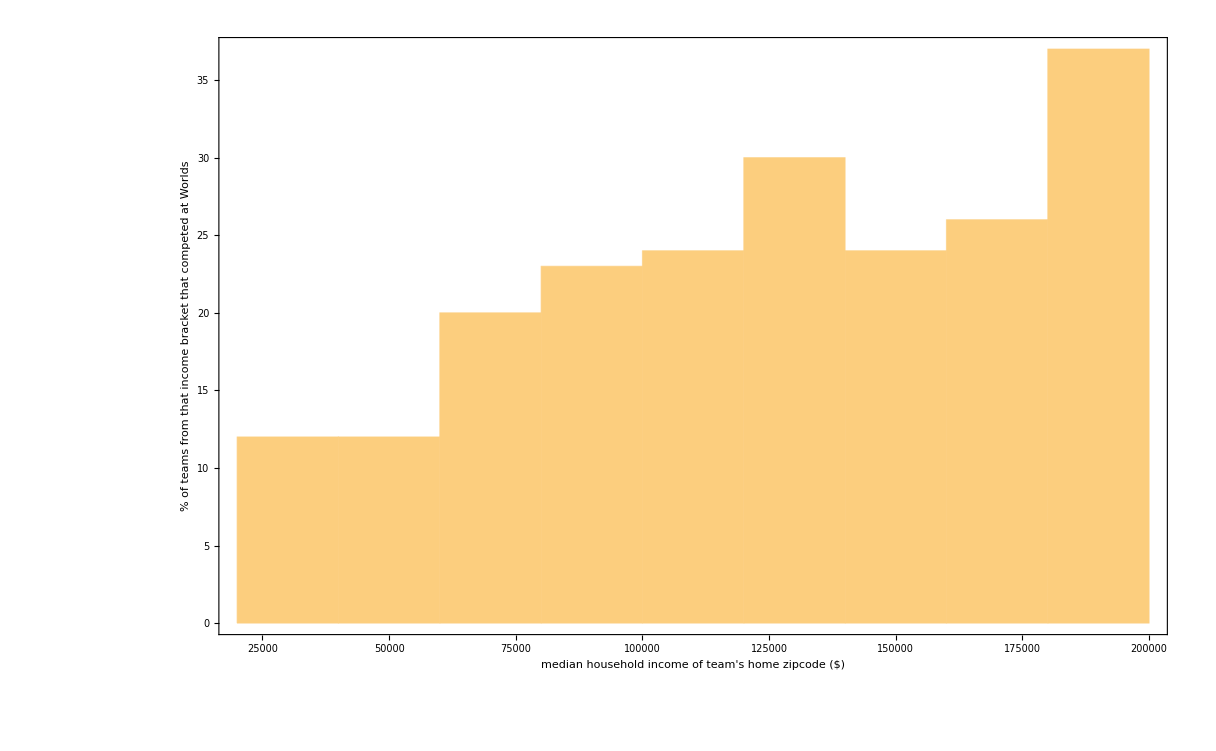

```mathematica
bin=20000;
percentagedata=Table[{n*bin,N[(dataset[Select[#income>n*bin&&#income<(n+1)*bin&&#qualified=="Y"&],"income"]//Length)/(dataset[Select[#income>n*bin&&#income<(n+1)*bin&],"income"]//Length),2]*100},{n,0,(200000/bin)}]
labels={{Style["% of teams from that income bracket that competed at Worlds",Bold],""},{Style["median household income of team's home zipcode ($)",Bold],Style["Economic Analysis of FRC Team Performance \n",{Bold,Large}]"(e.g. 30% of teams based in zipcodes with median household incomes between $100,000 and $110,000 competed at Worlds)"}};
Histogram[Flatten[Table[#[[1]],#[[2]]]&/@percentagedata],{bin,200000,bin},Frame->True,FrameLabel->labels,LabelStyle->"Subsection"]
```

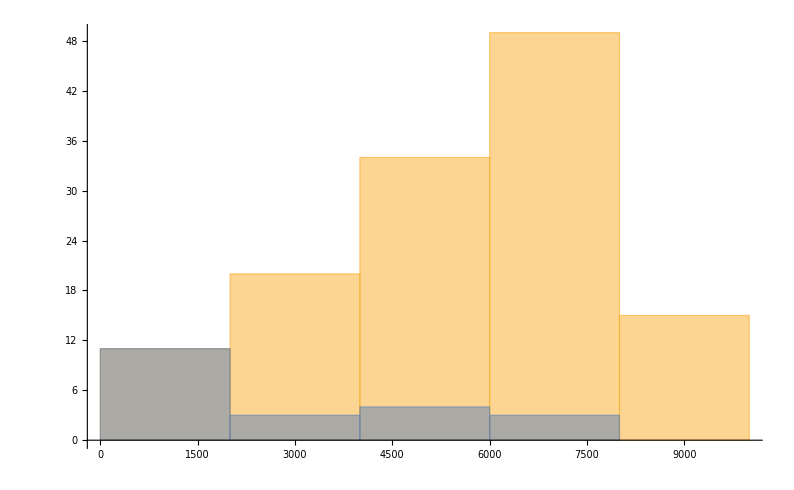

```mathematica
Histogram[{dataset[Select[#income>10000&&#income<30000&&#team<10000&&#qualified=="N"&],"team"]//Normal,dataset[Select[#income>10000&&#income<30000&&#team<10000&&#qualified=="Y"&],"team"]//Normal}]
```

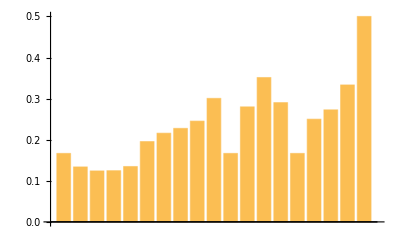

```mathematica
BarChart[percentagedata]
```

```mathematica
(* fix max number*)
```

```mathematica
qualifiedincome=dataset[Select[#qualified=="Y"&],"income"];
unqualifiedincome=dataset[Select[#qualified=="N"&],"income"];
```

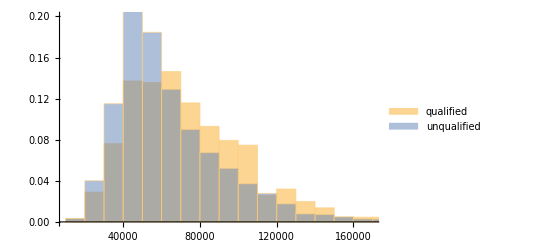

```mathematica
Histogram[{qualifiedincome//Normal,unqualifiedincome//Normal},{10000},Probability,PlotRange->{0,0.20},ChartLegends->{"qualified","unqualified"}]
```

```mathematica
(* zip code is from team-event search page of official FIRST website, income data is from 2017-adjusted US Gov. Census American Community Survey, list of qualifying teams is from 2018 championship event pages on FIRST official website*)
```

```mathematica
Export["fullycurateddata.xlsx",(dataset)//Normal//Normal]
```

fullycurateddata.xlsx

```mathematica
entries=List@@@Normal@dataset;
keys=dataset[1,Keys]//Normal

csvDataSet=PrependTo[entries,keys];

Export["text.csv",csvDataSet]
```

{team,zip,income,qualified}

text.csv

```mathematica
bin=20000;
percentagedata=Table[{n*bin,N[(dataset[Select[#income>n*bin&&#income<(n+1)*bin&&#qualified=="Y"&],"income"]//Length)/(dataset[Select[#income>n*bin&&#income<(n+1)*bin&],"income"]//Length),2]*100},{n,0,(200000/bin)}]
```

{{0,17.},{20000,13.},{40000,13.},{60000,20.},{80000,24.},{100000,25.},{120000,30.},{140000,24.},{160000,26.},{180000,38.},{200000,0}}

```mathematica
(* TESTING *)
```

{{0,13},{50000,19},{100000,26}}

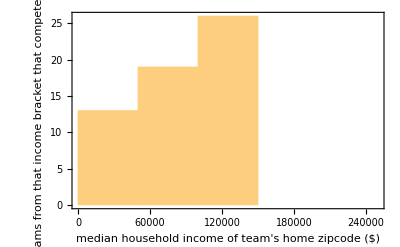

-Graphics-

{{50000,Indeterminate},{50000,Indeterminate},{50000,Indeterminate},{50000,Indeterminate},{50000,Indeterminate}}

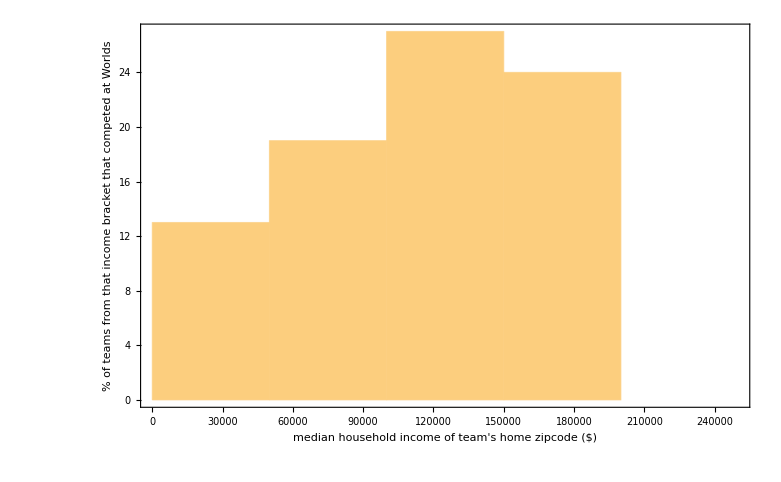

{{0,13},{50000,19},{100000,27},{150000,24},{200000,0}}

```mathematica
percentagedata=Table[{bin[[1]],Round[((dataset[Select[#income>bin[[1]]&&#income<bin[[2]]&&#qualified=="Y"&&#team<100000&],"income"]//Length)/(dataset[Select[#income>bin[[1]]&&#income<bin[[2]]&&#team<100000&],"income"]//Length))*100]},{bin,{{0,50000},{50000,100000},{100000,250000}}}]
labels={{Style["% of teams from that income bracket that competed at Worlds",Bold],""},{Style["median household income of team's home zipcode ($)",Bold],Style["Economic Analysis of FRC Team Performance \n",{Bold,Large}]"(e.g. 30% of teams based in zipcodes with median household incomes between $100,000 and $110,000 competed at Worlds)"}};
Histogram[Flatten[Table[#[[1]],#[[2]]]&/@percentagedata],{0,250000,bin},Frame->True,FrameLabel->labels,LabelStyle->"Subsection"]
```

```mathematica
dataset[Select[#income>100000&&#income<250000&&#team<100000&&#qualified=="Y"&],"income"]//Length
```

121

```mathematica
N[69/(476+69)]
```

0.126606

```mathematica
Table[#[[1]],#[[2]]]&/@{{10000,12}}
```

{{10000,10000,10000,10000,10000,10000,10000,10000,10000,10000,10000,10000}}

```mathematica
N[121/460]
```

0.214286

```mathematica
Table[ToString[interval[[1]]],{interval,{{1,2},{2,3},{3,4}}}]
```

{1,2,3}

```mathematica
(* V5 *)
```

```mathematica
percentqualify=Table[N[((dataset[Select[#income>bin[[1]]&&#income<bin[[2]]&&#qualified=="Y"&&#team<100000&],"income"]//Length)/(dataset[Select[#income>bin[[1]]&&#income<bin[[2]]&&#team<100000&],"income"]//Length))*100,4],{bin,{{0,50000},{50000,100000},{100000,250000}}}]
```

{12.88,19.16,26.3}

```mathematica
numberinbracket=AssociationThread[percentqualify,Table[(dataset[Select[#income>bin[[1]]&&#income<bin[[2]]&&#team<100000&],"income"]//Length),{bin,{{0,50000},{50000,100000},{100000,250000}}}]]
```

<|12.88→1250,19.16→1947,26.3→460|>

```mathematica
labels={{Style["% of teams from that income bracket that competed at Worlds",Bold],""},{Style["median household income of team's home zipcode ($)",Bold],Style["Economic Analysis of FRC Team Performance",{Bold,Large}]""}};
```

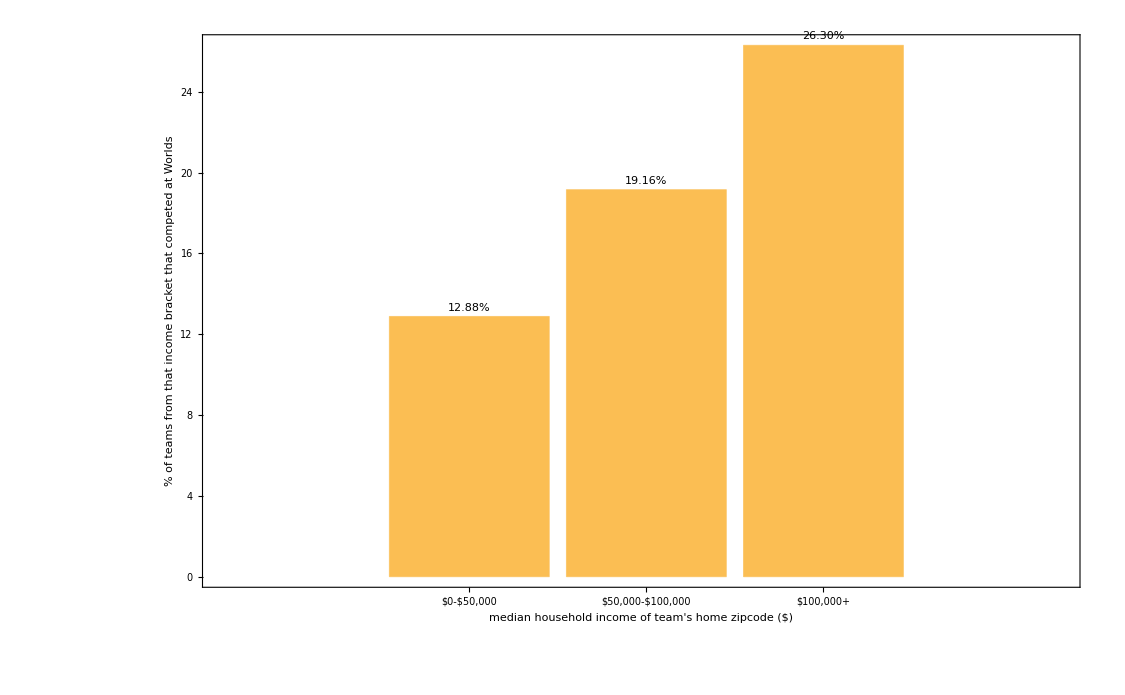

```mathematica
BarChart[percentqualify,ChartLabels->{"$0-$50,000","$50,000-$100,000","$100,000+"},LabelingFunction->(Placed[Style[ToString[#]<>"%" (* of "<>ToString[numberinbracket[#]]<>" teams"*)],Above]&),Frame->True,FrameLabel->labels,LabelStyle->"Subsection"]
```

Sources: 
	team number, home zipcode:  https://www.firstinspires.org/team-event-search #type=teams&sort=name&programs=FRC&year=2019&country=USA
	median household income by zipcode:  American Community Survey (US Census Bureau) -- ”ACS_17_5YR_DP03_with_ann”
	qualification for worlds:  https://frc-events.firstinspires.org/2018/CMPTX, https://frc-events.firstinspires.org/2018/CMPMI 
This data only reflects US Teams. Sample Size = 3,657.
Created using Mathematica and Excel. This chart is the product of over 4 weeks of work.

```mathematica
dataset[Select[#income>100000 &&#income<1000000&&#qualified=="Y"&&#team<100000&],"income"]//Length
```

121